```mathematica
Clear["Global`*"]
```

```mathematica
euler[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
ynew=yold+h*(f/.{x->xold,y->yold});
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
heun[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
slopeold=f/.{x->xold,y->yold};
slopenew=f/.{x->(xold+h),y->(yold+h*(f/.{x->xold,y->yold}))};
ynew=yold+0.5*h*(slopeold+slopenew);
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
RKA[f_,{x_,x0_,xn_},{y_,y0_},steps_]:=Block[{xold=x0,yold=y0,sollist={{x0,y0}},x,y,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
k1=h*f/.{x->xold,y->yold};
k2=h*f/.{x->(xold+0.5*h),y->(yold+0.5*k1)};
k3=h*f/.{x->(xold+0.5*h),y->(yold+0.5*k2)};
k4=h*f/.{x->(xold+h),y->(yold+k3)};
ynew=yold+(1.0/6.0)*(k1+2k2+2k3+k4);
sollist=Append[sollist,{xnew,ynew}];
xold=xnew;
yold=ynew,{steps}];
Return[sollist]]
```

```mathematica
func[x_,y_]:=2-E^(-4x)-2y
sol[x_]:=1+1/2 E^(-4x)-1/2 E^(-2x)
```

```mathematica
func[x_,y_]:=y-1/2 E^(x/2)Sin[5x]+5 E^(x/2)Cos[5x];
sol[x_]:=E^(x/2)Sin[5x];
```

```mathematica
x0=0;
y0=0;
x1=10;
npoints=100;
```

```mathematica
eulerex1=euler[func[x,y],{x,x0,x1},{y,y0},npoints];
heunex1=heun[func[x,y],{x,x0,x1},{y,y0},npoints];
RKAex1=RKA[func[x,y],{x,x0,x1},{y,y0},npoints];
```

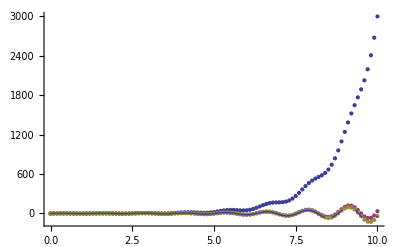

```mathematica
foo=ListPlot[{eulerex1,heunex1,RKAex1}];
bar=Plot[sol[x],{x,x0,x1}];
Show[foo,bar]
```

```mathematica
euler2[f1_,f2_,{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
y1new=y1old+h*(f1/.{x->xold,y1->y1old,y2-> y2old});
y2new=y2old+h*(f2/.{x->xold,y1->y1old,y2->y2old});
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
heun2[f1_,f2_,{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
slope1old=f1/.{x->xold,y1->y1old,y2-> y2old};
slope2old=f2/.{x->xold,y1->y1old,y2-> y2old};
slope1new=f1/.{x->(xold+h),y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
slope2new=f2/.{x->(xold+h),y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
y1new=y1old+0.5*h*(slope1old+slope1new);
y2new=y2old+0.5*h*(slope2old+slope2new);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
RKA2[f1_,f2_,{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
k11=h*f1/.{x->xold,y1->y1old,y2-> y2old};
k21=h*f2/.{x->xold,y1->y1old,y2-> y2old};
k12=h*f1/.{x->(xold+0.5*h),y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k22=h*f2/.{x->(xold+0.5*h),y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k13=h*f1/.{x->(xold+0.5*h),y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k23=h*f2/.{x->(xold+0.5*h),y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k14=h*f1/.{x->(xold+h),y1->(y1old+k13),y2-> (y2old+k23)};
k24=h*f2/.{x->(xold+h),y1->(y1old+k13),y2-> (y2old+k23)};
y1new=y1old+(1.0/6.0)*(k11+2k12+2k13+k14);
y2new=y2old+(1.0/6.0)*(k21+2k22+2k23+k24);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
func1[x_,y1_,y2_]:=y2;
func2[x_,y1_,y2_]:=-2y1;
sol1[x_]:=Sin[√2 x];
sol2[x_]:=√2 Cos[√2 x];
```

```mathematica
x0=1;
y10=0;
y20=√2;
x1=10;
npoints=100;
```

```mathematica
eulersol=euler2[func1[x,y1,y2],func2[x,y1,y2],{x,x0,x1},{y1,y10},{y2,y20},npoints];
eulersolpts1=Table[{eulersol[[i,1]],eulersol[[i,2]]},{i,1,Length[eulersol]}];
eulersolpts2=Table[{eulersol[[i,1]],eulersol[[i,3]]},{i,1,Length[eulersol]}];
heunsol=heun2[func1[x,y1,y2],func2[x,y1,y2],{x,x0,x1},{y1,y10},{y2,y20},npoints];
heunsolpts1=Table[{heunsol[[i,1]],heunsol[[i,2]]},{i,1,Length[heunsol]}];
heunsolpts2=Table[{heunsol[[i,1]],heunsol[[i,3]]},{i,1,Length[heunsol]}];
RKAsol=RKA2[func1[x,y1,y2],func2[x,y1,y2],{x,x0,x1},{y1,y10},{y2,y20},npoints];
RKAsolpts1=Table[{RKAsol[[i,1]],RKAsol[[i,2]]},{i,1,Length[RKAsol]}];
RKAsolpts2=Table[{RKAsol[[i,1]],RKAsol[[i,3]]},{i,1,Length[RKAsol]}];
```

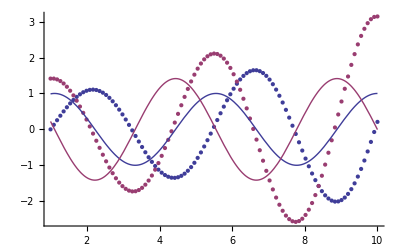

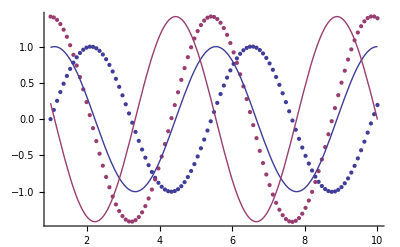

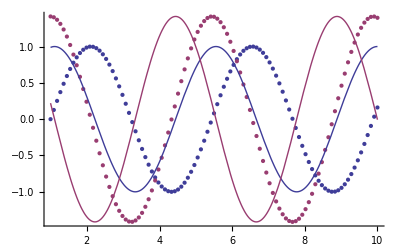

```mathematica
eulerplot=ListPlot[{eulersolpts1,eulersolpts2}];
heunplot=ListPlot[{heunsolpts1,heunsolpts2}];
RKAplot=ListPlot[{RKAsolpts1,RKAsolpts2}];
bar=Plot[{sol1[x],sol2[x]},{x,x0,x1}];
Show[eulerplot,bar]
Show[heunplot,bar]
Show[RKAplot,bar]
```

```mathematica
euler3[{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{i=0,xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[i+=1;
xnew=xold+h;
y1new=y1old+h*(C1t[[i]]y2)/.{y1->y1old,y2-> y2old};
y2new=y2old+h*(C2t[[i]]y1)/.{y1->y1old,y2-> y2old};
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
heun3[{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{i=0,xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[i+=1;
xnew=xold+h;
y1new=y1old+h*(C1t[[i]]y2/.{y1->y1old,y2-> y2old});
y2new=y2old+h*(C2t[[i]]y1/.{y1->y1old,y2->y2old});
slope1old=C1t[[i]]y2/.{y1->y1old,y2-> y2old};
slope2old=C2t[[i]]y1/.{y1->y1old,y2-> y2old};
slope1new=C1t[[i+1]]y2/.{y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
slope2new=C2t[[i+1]]y1/.{y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
y1new=y1old+0.5*h*(slope1old+slope1new);
y2new=y2old+0.5*h*(slope2old+slope2new);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
RKA3[{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{i=0,xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[i+=1;
xnew=xold+h;
k11=h*C1t[[i]]y2/.{y1->y1old,y2-> y2old};
k21=h*C2t[[i]]y1/.{y1->y1old,y2-> y2old};
k12=h*0.5(C1t[[i]]+C1t[[i+1]])y2/.{y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k22=h*0.5(C2t[[i]]+C2t[[i+1]])y1/.{y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k13=h*0.5(C1t[[i]]+C1t[[i+1]])y2/.{y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k23=h*0.5(C2t[[i]]+C2t[[i+1]])y1/.{y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k14=h*C1t[[i+1]]y2/.{y1->(y1old+k13),y2-> (y2old+k23)};
k24=h*C2t[[i+1]]y1/.{y1->(y1old+k13),y2-> (y2old+k23)};
y1new=y1old+(1.0/6.0)*(k11+2k12+2k13+k14);
y2new=y2old+(1.0/6.0)*(k21+2k22+2k23+k24);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
x0=0;
y10=0;
y20=√2;
x1=10;
npoints=100;
```

```mathematica
C1t=Table[1,{i,1,npoints+1}];
C2t=Table[-2,{i,1,npoints+1}];
dx=N[(x1-x0)/npoints];
sol1[x_]:=Sin[√2 x];
sol2[x_]:=√2 Cos[√2 x];
```

```mathematica
eulersol=euler3[{x,x0,x1},{y1,y10},{y2,y20},npoints];
eulersolpts1=Table[{eulersol[[i,1]],eulersol[[i,2]]},{i,1,Length[eulersol]}];
eulersolpts2=Table[{eulersol[[i,1]],eulersol[[i,3]]},{i,1,Length[eulersol]}];
heunsol=heun3[{x,x0,x1},{y1,y10},{y2,y20},npoints];
heunsolpts1=Table[{heunsol[[i,1]],heunsol[[i,2]]},{i,1,Length[heunsol]}];
heunsolpts2=Table[{heunsol[[i,1]],heunsol[[i,3]]},{i,1,Length[heunsol]}];
RKAsol=RKA3[{x,x0,x1},{y1,y10},{y2,y20},npoints];
RKAsolpts1=Table[{RKAsol[[i,1]],RKAsol[[i,2]]},{i,1,Length[RKAsol]}];
RKAsolpts2=Table[{RKAsol[[i,1]],RKAsol[[i,3]]},{i,1,Length[RKAsol]}];
```

```mathematica
eulerplot=ListPlot[{eulersolpts1,eulersolpts2}];
heunplot=ListPlot[{heunsolpts1,heunsolpts2}];
RKAplot=ListPlot[{RKAsolpts1,RKAsolpts2}];
bar=Plot[{sol1[x],sol2[x]},{x,x0,x1}];
Show[eulerplot,bar]
Show[heunplot,bar]
Show[RKAplot,bar]
```

## Old

```mathematica
f1=epoints[0]-3efuncpoints[1];
f2=epoints[1]-3efuncpoints[3];
```

Thread::tdlen: Objects of unequal length in {66.9076`, 40.0975`, 31.2631`, 21.4876`, 19.3347`, 15.1822`, 12.4985`, 11.5132`, 10.3369`, 9.62629`, 6.60087`, 4.86357`, 3.98846`, 3.23416`, 2.908`, 2.62188`, 2.3975`, 2.30361`, 2.13382`} + {-9.737790361823937`, -5.908658784746992`, -4.971561268421304`, -4.667916243273966`, -4.561052894156737`, -4.522364204911602`, -4.508214428278995`, -4.503020176807571`, -4.501110825323515`, -4.500408617919087`} cannot be combined.

Thread::tdlen: Objects of unequal length in {0, 0, 0, 0, 0, 0, 0.0117934`, 0.00797461`, 0.0329294`, 0.0492297`, 0.416994`, 1.60711`, 2.28235`, 2.99992`, 3.2238`, 3.46372`, 3.59709`, 3.68662`, 3.79985`} + {-4.971561268421304`, -4.522364204911602`, -4.501110825323515`, -9/2, -9/2, -9/2, -9/2, -9/2, -9/2, -9/2} cannot be combined.

```mathematica
g1=-2 zfuncpoints[3]/zfuncpoints[1]^3 epoints[0];
g2=-1/2 zfuncpoints[1]^3/zfuncpoints[3] epoints[1];
```

Thread::tdlen: Objects of unequal length in -2 {0.018781766145723647`, 0.27218436420642733`, 0.6317557846381738`, 0.8467493213682205`, 0.9409683001809669`, 0.9779111921620247`, 0.9918229359935979`, 0.9969848845585606`, 0.9988898598902715`, 0.999591474826088`} {66.9076`, 40.0975`, 31.2631`, 21.4876`, 19.3347`, 15.1822`, 12.4985`, 11.5132`, 10.3369`, 9.62629`, 6.60087`, 4.86357`, 3.98846`, 3.23416`, 2.908`, 2.62188`, 2.3975`, 2.30361`, 2.13382`} cannot be combined.

Thread::tdlen: Objects of unequal length in -1/2 {53.24312912008471`, 3.6739803291624424`, 1.5828901362141559`, 1.180987069920705`, 1.0627350568639562`, 1.0225877441786304`, 1.0082444796441516`, 1.003024233855636`, 1.0011113738904613`, 1.0004086921349373`} {0, 0, 0, 0, 0, 0, 0.0117934`, 0.00797461`, 0.0329294`, 0.0492297`, 0.416994`, 1.60711`, 2.28235`, 2.99992`, 3.2238`, 3.46372`, 3.59709`, 3.68662`, 3.79985`} cannot be combined.

```mathematica
euler[{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{i=0,xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[i+=1;
xnew=xold+h;
y1new=y1old+h*(g1[[i]]y2-f1[[i]]y1)/.{y1->y1old,y2-> y2old};
y2new=y2old+h*(g2[[i]]y1-f2[[i]]y2)/.{y1->y1old,y2-> y2old};
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps-1}];
Return[sollist]]
```

```mathematica
heun[{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{i=0,xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[i+=1;
xnew=xold+h;
slope1old=g1[[i]]y2-f1[[i]]y1/.{y1->y1old,y2-> y2old};
slope2old=g2[[i]]y1-f2[[i]]y2/.{y1->y1old,y2-> y2old};
slope1new=g1[[i+1]]y2-f1[[i+1]]y1/.{y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
slope2new=g2[[i+1]]y1-f2[[i+1]]y2/.{y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
y1new=y1old+0.5*h*(slope1old+slope1new);
y2new=y2old+0.5*h*(slope2old+slope2new);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps-1}];
Return[sollist]]
```

```mathematica
RKA[{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{i=0,xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[i+=1;
xnew=xold+h;
k11=h*(g1[[i]]y2-f1[[i]]y1)/.{y1->y1old,y2-> y2old};
k21=h*(g2[[i]]y1-f2[[i]]y2)/.{y1->y1old,y2-> y2old};
k12=h*0.5((g1[[i]]+g1[[i+1]])y2-(f1[[i]]+f1[[i+1]])y1)/.{y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k22=h*0.5((g2[[i]]+g2[[i+1]])y1-(f2[[i]]+f2[[i+1]])y2)/.{y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k13=h*0.5((g1[[i]]+g1[[i+1]])y2-(f1[[i]]+f1[[i+1]])y1)/.{y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k23=h*0.5((g2[[i]]+g2[[i+1]])y1-(f2[[i]]+f2[[i+1]])y2)/.{y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k14=h*(g1[[i+1]]y2-f1[[i+1]]y1)/.{y1->(y1old+k13),y2-> (y2old+k23)};
k24=h*(g2[[i+1]]y1-f2[[i+1]]y2)/.{y1->(y1old+k13),y2-> (y2old+k23)};
y1new=y1old+(1.0/6.0)*(k11+2k12+2k13+k14);
y2new=y2old+(1.0/6.0)*(k21+2k22+2k23+k24);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps-1}];
Return[sollist]]
```

```mathematica
y10=1.0;
y20=0.0;
```

```mathematica
eulersol=euler[{x,βmin,βmax},{y1,y10},{y2,y20},nPoints];
eulersolpts1=Table[{eulersol[[i,1]],eulersol[[i,2]]},{i,1,Length[eulersol]}];
eulersolpts2=Table[{eulersol[[i,1]],eulersol[[i,3]]},{i,1,Length[eulersol]}];
```

Thread::tdlen: Objects of unequal length in {0.018781766145723647` y2, 0.27218436420642733` y2, 0.6317557846381738` y2, 0.8467493213682205` y2, 0.9409683001809669` y2, 0.9779111921620247` y2, 0.9918229359935979` y2, 0.9969848845585606` y2, 0.9988898598902715` y2, 0.999591474826088` y2} + {-66.9076` y1, -40.0975` y1, -31.2631` y1, -21.4876` y1, -19.3347` y1, -15.1822` y1, -12.4985` y1, -11.5132` y1, -10.3369` y1, -9.62629` y1, -6.60087` y1, -4.86357` y1, -3.98846` y1, -3.23416` y1, -2.908` y1, -2.62188` y1, -2.3975` y1, -2.30361` y1, -2.13382` y1} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`}, « 8 », {-0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`}} + {{-653.2865641714942`, -422.70836065570404`, « 7 », -337.9079856798548`}, {« 1 »}, « 16 », {« 1 »}} cannot be combined.

General::stop: Further output of Thread will be suppressed during this calculation.

Part::partw: Part 3 of {-9.737790361823937`, -5.908658784746992`, -4.971561268421304`, -4.667916243273966`, -4.561052894156737`, -4.522364204911602`, -4.508214428278995`, -4.503020176807571`, -4.501110825323515`, -4.500408617919087`} + {66.9076`, 40.0975`, 31.2631`, 21.4876`, 19.3347`, 15.1822`, 12.4985`, 11.5132`, 10.3369`, 9.62629`, 6.60087`, 4.86357`, 3.98846`, 3.23416`, 2.908`, 2.62188`, 2.3975`, 2.30361`, 2.13382`} does not exist.

Part::partw: Part 3 of {-4.971561268421304`, -4.522364204911602`, -4.501110825323515`, -9/2, -9/2, -9/2, -9/2, -9/2, -9/2, -9/2} + {0, 0, 0, 0, 0, 0, 0.0117934`, 0.00797461`, 0.0329294`, 0.0492297`, 0.416994`, 1.60711`, 2.28235`, 2.99992`, 3.2238`, 3.46372`, 3.59709`, 3.68662`, 3.79985`} does not exist.

Part::partw: Part 4 of -2 {0.018781766145723647`, 0.27218436420642733`, 0.6317557846381738`, 0.8467493213682205`, 0.9409683001809669`, 0.9779111921620247`, 0.9918229359935979`, 0.9969848845585606`, 0.9988898598902715`, 0.999591474826088`} {66.9076`, 40.0975`, 31.2631`, 21.4876`, 19.3347`, 15.1822`, 12.4985`, 11.5132`, 10.3369`, 9.62629`, 6.60087`, 4.86357`, 3.98846`, 3.23416`, 2.908`, 2.62188`, 2.3975`, 2.30361`, 2.13382`} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

```mathematica
heunsol=heun[{x,βmin,βmax},{y1,y10},{y2,y20},nPoints];
heunsolpts1=Table[{heunsol[[i,1]],heunsol[[i,2]]},{i,1,Length[heunsol]}];
heunsolpts2=Table[{heunsol[[i,1]],heunsol[[i,3]]},{i,1,Length[heunsol]}];
```

Thread::tdlen: Objects of unequal length in {0.018781766145723647` y2, 0.27218436420642733` y2, 0.6317557846381738` y2, 0.8467493213682205` y2, 0.9409683001809669` y2, 0.9779111921620247` y2, 0.9918229359935979` y2, 0.9969848845585606` y2, 0.9988898598902715` y2, 0.999591474826088` y2} + {-66.9076` y1, -40.0975` y1, -31.2631` y1, -21.4876` y1, -19.3347` y1, -15.1822` y1, -12.4985` y1, -11.5132` y1, -10.3369` y1, -9.62629` y1, -6.60087` y1, -4.86357` y1, -3.98846` y1, -3.23416` y1, -2.908` y1, -2.62188` y1, -2.3975` y1, -2.30361` y1, -2.13382` y1} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`, -0.008451794765575641`}, « 8 », {-0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`, -0.4498161636717396`}} + {{-653.2865641714942`, -422.70836065570404`, « 7 », -337.9079856798548`}, {« 1 »}, « 16 », {« 1 »}} cannot be combined.

Thread::tdlen: Objects of unequal length in {53.24312912008471` y1, 3.6739803291624424` y1, 1.5828901362141559` y1, 1.180987069920705` y1, 1.0627350568639562` y1, 1.0225877441786304` y1, 1.0082444796441516` y1, 1.003024233855636` y1, 1.0011113738904613` y1, 1.0004086921349373` y1} + {0, 0, 0, 0, 0, 0, -0.0117934` y2, -0.00797461` y2, -0.0329294` y2, -0.0492297` y2, -0.416994` y2, -1.60711` y2, -2.28235` y2, -2.99992` y2, -3.2238` y2, -3.46372` y2, -3.59709` y2, -3.68662` y2, -3.79985` y2} cannot be combined.

General::stop: Further output of Thread will be suppressed during this calculation.

Part::partw: Part 3 of {-9.737790361823937`, -5.908658784746992`, -4.971561268421304`, -4.667916243273966`, -4.561052894156737`, -4.522364204911602`, -4.508214428278995`, -4.503020176807571`, -4.501110825323515`, -4.500408617919087`} + {66.9076`, 40.0975`, 31.2631`, 21.4876`, 19.3347`, 15.1822`, 12.4985`, 11.5132`, 10.3369`, 9.62629`, 6.60087`, 4.86357`, 3.98846`, 3.23416`, 2.908`, 2.62188`, 2.3975`, 2.30361`, 2.13382`} does not exist.

Part::partw: Part 3 of {-4.971561268421304`, -4.522364204911602`, -4.501110825323515`, -9/2, -9/2, -9/2, -9/2, -9/2, -9/2, -9/2} + {0, 0, 0, 0, 0, 0, 0.0117934`, 0.00797461`, 0.0329294`, 0.0492297`, 0.416994`, 1.60711`, 2.28235`, 2.99992`, 3.2238`, 3.46372`, 3.59709`, 3.68662`, 3.79985`} does not exist.

Part::partw: Part 3 of {-9.737790361823937`, -5.908658784746992`, -4.971561268421304`, -4.667916243273966`, -4.561052894156737`, -4.522364204911602`, -4.508214428278995`, -4.503020176807571`, -4.501110825323515`, -4.500408617919087`} + {66.9076`, 40.0975`, 31.2631`, 21.4876`, 19.3347`, 15.1822`, 12.4985`, 11.5132`, 10.3369`, 9.62629`, 6.60087`, 4.86357`, 3.98846`, 3.23416`, 2.908`, 2.62188`, 2.3975`, 2.30361`, 2.13382`} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

```mathematica
RKAsol=RKA[{x,βmin,βmax},{y1,y10},{y2,y20},nPoints];
RKAsolpts1=Table[{RKAsol[[i,1]],RKAsol[[i,2]]},{i,1,Length[RKAsol]}];
RKAsolpts2=Table[{RKAsol[[i,1]],RKAsol[[i,3]]},{i,1,Length[RKAsol]}]
```

{{1.,0.},{1.9,-1.10574},{2.8,-38.8192},{3.7,-1326.28},{4.6,-46103.5},{5.5,-1.62619×10^6},{6.4,-5.76088×10^7},{7.3,-2.04469×10^9},{8.2,-7.26229×10^10},{9.1,-2.58009×10^12}}

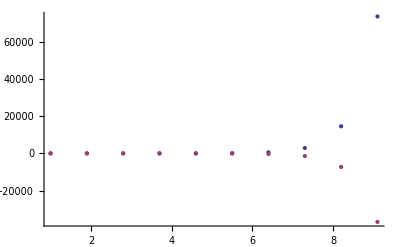

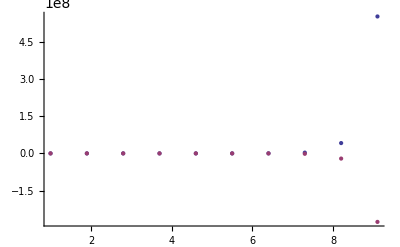

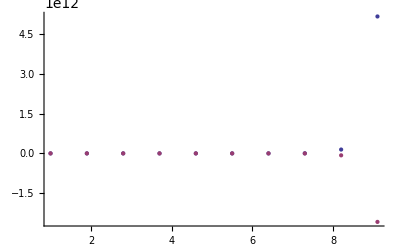

```mathematica
eulerplot=ListPlot[{eulersolpts1,eulersolpts2}];
heunplot=ListPlot[{heunsolpts1,heunsolpts2}];
RKAplot=ListPlot[{RKAsolpts1,RKAsolpts2}];
Show[eulerplot]
Show[heunplot]
Show[RKAplot]
```

```mathematica
Export["omega/f1.dat",Table[{βmin +dβ*(i-1),f1[[i]]},{i,1,nPoints}]];
Export["omega/f2.dat",Table[{βmin +dβ*(i-1),f2[[i]]},{i,1,nPoints}]];
Export["omega/g1.dat",Table[{βmin +dβ*(i-1),g1[[i]]},{i,1,nPoints}]];
Export["omega/g2.dat",Table[{βmin +dβ*(i-1),g2[[i]]},{i,1,nPoints}]];
```